# Auto-grader for Open Ended Math Problems

### Determining Equivalent Responses and Classifying Problems for Proper Evaluation of student response

Silas Kurt Grossberndt
Robert Nachbar

#### Abstract

In order to automatically grade student problems one must identify the scope and level of the problem and then define equivalent answers appropriate to the context of the question and knowledge of the student. To this end, we first train a Neural Network Classifier on a data set of problems in Algebra 1, Algebra 2 and Calculus. Then, using a combination of rule based checks and the theorem prover, we define equivalent answers, then check that particular rules were not used in order to maintain equivalence at the level of the student to prevent cheating.

## Introduction

When providing questions to students online, the teacher is often left with a dilemma. Do  you give the student a multiple choice problem that fails to properly test their ability by allowing guessing, or do you give them a long answer that will only accept one correct answer, when there might be multiple equivalent answers? To add in all possible answers would be an onerous task, thus it would be preferable to have the system automatically identify all possible answers. However, this presents a challenge in its own right. How does one limit the possible answers to those that the student would have reached based on the level of their knowledge, and how does one deal with problems that may limit the scope of the equivalent answers? To this end, we define a two part problem: classification of the problem’s level and scope and cross checking for equivalent answers.

## Classifying and Identifying Problems

### Classifying Questions to determine the level of the problem

The problem of classification is often solved by machine learning techniques trained on large data sets. In this case, I retrained a series of models in the Wolfram language “Classify” function on a 1800 question data set in algebra 1, 2  and calculus, grouping all the problems and providing the problems and groupings to the network, i.e. training in a supervised manner. Then, the accuracy of each model was tested by comparing the probability of identification as the proper grouping to the highest probability of the other two groups, using:

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs|> , PerformanceGoal->"Quality", Method->"Markov"]


algebra1IsAlgebra1=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
algebra1IsAlgebra2=questionClassifier[algebra1Questions, {"Probability", "algebra 2"}];

algebra2IsAlgebra1=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
algebra2IsAlgebra2=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];

lp=ListLogPlot[#right/#wrong&@ <|"right"-> algebra1IsAlgebra1, "wrong"-> algebra1IsAlgebra2|>,AxesLabel->{"Data"},PlotLabel->"Algebra 1 ", GridLines->{{}, {1}}, GridLinesStyle->Red] ;
lp1=ListLogPlot[#right/#wrong&@ <|"right"-> algebra2IsAlgebra2, "wrong"-> algebra2IsAlgebra1|>,AxesLabel->{"Data"}, PlotLabel->"Algebra 2",GridLines->{{}, {1}}, GridLinesStyle->Red];
```

ClassifierFunction[…]

All models were given the “Quality” goal to improve accuracy at the cost of training time, as the training is taking place ahead of time, and the system is not retrained live. However, when this was performed on data generated by the Wolfram|Alpha Problem Generator, where the addition of calculus made “What is 1+1” evaluate as calculus independent of the number of inputs. Total training inputs are 1302, with 651 each of algebra 1 and 2.

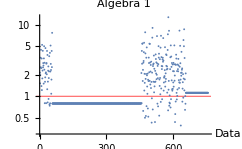
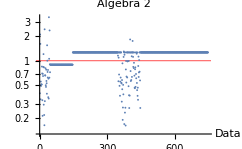
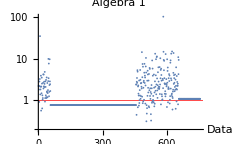
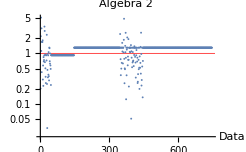
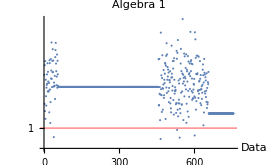
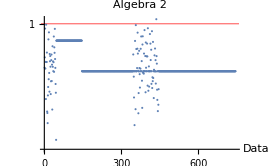
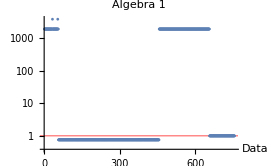
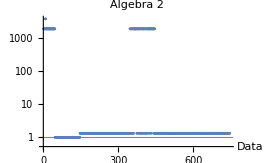
Method | Algebra1  | Algebra 2 | Accuracy
Automatic | -Graphics- | -Graphics- | 0.58
Neural Network | -Graphics- | -Graphics- | 0.59
Logistic Regression | -Graphics- | -Graphics- | 0.50
Naive Bayesian | -Graphics- | -Graphics- | 0.67
Nearest Neighbor | -Graphics- | -Graphics- | 0.57
Gradiant Boosted Trees | -Graphics- | -Graphics- | 0.59
Markov | -Graphics- | -Graphics- | 0.93
Support Vector Machine | -Graphics- | -Graphics- | 0.57
Random Forest | -Graphics- | -Graphics- | 0.63
Decision Tree | -Graphics- | -Graphics- | 0.50

It is thus obvious to select the Markov model for the classifier.

### Identifying the Context of the Problem

The context of the problem, however, does not get captured by the classifier above. The classifier simply finds the level, meanwhile the context, for example, would be “write your answer as a simplified fraction”. These contexts are identified via pattern matching. These rules are then used to assign a specific tag:

Value | Meaning
0 | No Context Restrictions
1 | Simplest Form Fraction
2 | Decimal Representation
3 | A set of Points
4 | Calculus
5 | A set of Points of Simplest Fractions
6 | A set of Points in Decimal
7 | Mixed Number
8 | Improper Fraction

The rules were given by :

```mathematica
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrixQ[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalcQ[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
```

Note that the calculus rule here will serve as the classifier for calculus, which is likely to leave a gap of problems given symbolically. One method to deal with this is discussed in the conclusion.

## Identifying Equivalent Responses

In order to provide a more robust and deployable version of the autograder, the identification of context and equivalent responses are handled in a new package, “Math Autograder”.

### Rule Based Identification

In order to perform checks on the context restricted identification, one performs the following for tags 1,2,7 and 8:

```mathematica
1|2|7|8, If[correctAnswer[answer, correct], True, False],
```

And for tags 5 and 6, one does the following to check if the data are equivalent except for ordering of the points:

```mathematica
5|6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False
```

### Theorem Prover Based Identification

In the majority of cases, the first test is still rule based:

```mathematica
correctAnswer[answer_, correct_]:=MatchQ[Interpreter["MathExpression"][answer], Interpreter["MathExpression"][correct]]
```

In order to reject answers that would give false positive, or answers that would be beyond the level of the student, we also implement the theorem prover:

```mathematica
If[correctAnswer[answer, correct], True, If[Simplify[Interpreter["MathExpression"][answer]- Interpreter["MathExpression"][correct]]==0, 
					If[UnsameQ[Head[Interpreter["MathExpression"][answer]], Failure], 
						formattedanswer:=removeProperFormat[Interpreter["MathExpression"][answer]];
						formattedcorrectanswer=removeProperFormat[Interpreter["MathExpression"][correct]];
						proof=TimeConstrained[FindEquationalProof[formattedanswer==formattedcorrectanswer , theorems[level]],1];
							If[proof["Logic"]=="EquationalLogic", 
								If[Complement[Query[Key[{"SubstitutionLemma", All}proof["ProofDataset"]["Statement"]]], theorems[level]]=={}, True, False],
								False],
						False],
					False]],
```

Wherein the formatting replacement is necessary to allow for the use of the defined axioms:

```mathematica
algebratheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n]} (*This defines an abelian ring w/ distributive property*)
```

```mathematica
algebraandtrigtheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n], 
				 ForAll[{a,b}, sin[g[a,b]]==g[f[sin[a],cos[b]], f[sin[b], cos[a]]]],
				 ForAll[ {a,b}, cos[g[a,b]]==g[f[cos[a],cos[b]], f[sin[inv[b]], sin[a]]]],
				 ForAll[a, sin[inv[a]]==inv[sin[a]]],
				 ForAll[a, cos[inv[a]]==cos[a]],
				 ForAll[a, g[f[sin[a],sin[a]], f[cos[a], cos[a]]]==n]}
```

All higher power terms would be picked up by the correct answer rule prover. There is the possibility of edge cases causing failure involving logarithms, but that is beyond the scope of this work. The conversion from the Wolfram Language input to the format required for this is done by:

```mathematica
removeSinCos[given_]:=given/.{Sin->sin, Cos->cos} 
removeSinCos[Sin[5]+Cos[x]]
replacePlus[given_]:=given/.{Plus-> g, Times[-1, amin_]->inv[amin]}
replacePlus[a-b]
replaceMulti[given_]:=given/.{Times-> f, Power[adiv_, -1]-> inv1[adiv]}
replaceTanSecCscCot[given_]:=given/.{Tan[atan_]-> f[sin[atan],inv1[cos[atan]]], Sec[asec_]-> inv1[cos[asec]], Csc[acsc_]-> inv1[sin[acsc]], Cot[acot_]-> f[inv1[sin[acot]],cos[acot]]}
replaceTanSecCscCot[Tan[y]+ Csc[x]]
removeProperFormat[given_]:=replacePlus[replaceMulti[removeSinCos[replaceTanSecCscCot[given]]]]
```

## Future work and Conclusions

This project has developed a Classifier and a Package that may be implemented in a variety of applications. Ideally, one can consider two exemplars. One has the student submits an answer to a randomly selected question from a database that has been built using Wolfram|Alpha’s Problem Generator. The student may select one of the three levels, receive a question, submit an answer and check that it is correct. After the correct answer has been submitted, the system automatically pulls a new question from the list in the selected type. The second allows for the teacher to create a quiz and store it as a new database, which will then be fed to the first exemplar. Thus, we see this project as a quiet sever side application, and as a service that would be deliverable to a client. Further work could encompass the addition of further levels of question, the use of graphical data as a selected answer or the inclusion of a retraining function in the neural net to improve classification accuracy, as well as the integration of the data into the described GUIs.

## Exemplar Implementation

The following is an example of asking a defined question (to avoid adding extra data to this presentation by adding in the question set), and checking if the answer is correct:

```mathematica
level=questionClassifier["What is 1+1"]
checkforEquivlentanswers["What is 1+1", "2" ,"3", level]
```

algebra 1

False

```mathematica
level=questionClassifier["How else can we write c*(a+b)"]
checkforEquivlentanswers["How else can we write c*(a+b)", "a*c+b*c", "c*a+b*c",level]
```

algebra 1

True

```mathematica
Question="";
Answer="";
CorrectAnswer="";
checkforEquivlentanswers[Question, Answer, CorrectAnswer, questionClassifier[Question]]
```

## Initialization Cells

```mathematica
correctAnswer[answer_, correct_]:=MatchQ[Interpreter["MathExpression"][answer], Interpreter["MathExpression"][correct]]
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrix[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalc[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
(*This is the wrong way to do it, patern matching is better here*)
expandToSix[answer_, correct_, x_]:=If[Series[answer, {x, 0, 6}]==Series[correct, {x, 0, 6}], True, False]
algebratheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n]} (*This defines an abelian ring w/ distributive property*)
				 
algebraandtrigtheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n], 
				 ForAll[{a,b}, sin[g[a,b]]==g[f[sin[a],cos[b]], f[sin[b], cos[a]]]],
				 ForAll[ {a,b}, cos[g[a,b]]==g[f[cos[a],cos[b]], f[sin[inv[b]], sin[a]]]],
				 ForAll[a, sin[inv[a]]==inv[sin[a]]],
				 ForAll[a, cos[inv[a]]==cos[a]],
				 ForAll[a, g[f[sin[a],sin[a]], f[cos[a], cos[a]]]==n]}
theorems=<|"algebra 1"-> {algebratheorems}, "algebra 2"-> {algebraandtrigtheorems}, "calc"-> {algebraandtrigtheorems}|>;
removeSinCos[given_]:=given/.{Sin->sin, Cos->cos} 
removeSinCos[Sin[5]+Cos[x]]
replacePlus[given_]:=given/.{Plus-> g, Times[-1, amin_]->inv[amin]}
replacePlus[a-b]
replaceMulti[given_]:=given/.{Times-> f, Power[adiv_, -1]-> inv1[adiv]}
replaceTanSecCscCot[given_]:=given/.{Tan[atan_]-> f[sin[atan],inv1[cos[atan]]], Sec[asec_]-> inv1[cos[asec]], Csc[acsc_]-> inv1[sin[acsc]], Cot[acot_]-> f[inv1[sin[acot]],cos[acot]]}
replaceTanSecCscCot[Tan[y]+ Csc[x]]
removeProperFormat[given_]:=replacePlus[replaceMulti[removeSinCos[replaceTanSecCscCot[given]]]]
determinetags[question_]:=If[allpoints[question], 
									If[turnOffEquivFrac[question], 5, 
												If[decForm[question], 6, 3]],
									If[turnOffEquivFrac[question], 1, 
											If[decForm[question], 2, 
												If[isCalc[question], 4, 
													If[mixedNumber[question], 7, 
														If[improperFraction[question], 8, 0]
													   ]
													]
												]
											]
								]; 


equivalentAnswer[level_, tags_, answer_, correct_]:=
Module[{formattedanswer, formattedcorrectanswer, proof}, 
			
				If[tags==4, level="calc"];
				Switch[tags, 
				0| 3| 4, If[correctAnswer[answer, correct], True, If[Simplify[Interpreter["MathExpression"][answer]- Interpreter["MathExpression"][correct]]==0, 
					If[UnsameQ[Head[Interpreter["MathExpression"][answer]], Failure], 
						formattedanswer:=removeProperFormat[Interpreter["MathExpression"][answer]];
						formattedcorrectanswer=removeProperFormat[Interpreter["MathExpression"][correct]];
						proof=TimeConstrained[FindEquationalProof[formattedanswer==formattedcorrectanswer , theorems[level]],10];
							If[proof["Logic"]=="EquationalLogic", 
								If[Complement[Query[Key[{"SubstitutionLemma", All}proof["ProofDataset"]["Statement"]]], theorems[level]]=={}, True, False],
								False],
						False],
					False]],
				1, If[correctAnswer[answer, correct], True, False], 
				2, If[correctAnswer[answer, correct], True, False], 
				5, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],  
				6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],
				_, MatchQ[answer, correct] (*exact match is default case*)
				
				]] 
				
checkforEquivlentanswers[question_, answer_, correct_, level_]:=
Module[{t},
			t=determinetags[question];
			equivalentAnswer[level, t, answer, correct]]	
equivalentAnswer["algebra 1", 7, "1 1/4", "5/4"]
```

{∀_{a,b,c}g[a,g[b,c]]==g[g[a,b],c],∀_{a,b}g[a,b]==g[b,a],∀_{a,b}f[a,b]==f[b,a],∀_{a,b,c}f[a,f[b,c]]==f[f[a,b],c],∀_{a,b,c}f[a,g[c,b]]==g[f[a,c],f[a,b]],∀_a g[a,e]==a,∀_a f[a,e]==e,∀_a f[a,n]==a,∀_a g[a,inv[a]]==e,∀_a f[a,inv1[a]]==n}

{∀_{a,b,c}g[a,g[b,c]]==g[g[a,b],c],∀_{a,b}g[a,b]==g[b,a],∀_{a,b}f[a,b]==f[b,a],∀_{a,b,c}f[a,f[b,c]]==f[f[a,b],c],∀_{a,b,c}f[a,g[c,b]]==g[f[a,c],f[a,b]],∀_a g[a,e]==a,∀_a f[a,e]==e,∀_a f[a,n]==a,∀_a g[a,inv[a]]==e,∀_a f[a,inv1[a]]==n,∀_{a,b}sin[g[a,b]]==g[f[sin[a],cos[b]],f[sin[b],cos[a]]],∀_{a,b}cos[g[a,b]]==g[f[cos[a],cos[b]],f[sin[inv[b]],sin[a]]],∀_a sin[inv[a]]==inv[sin[a]],∀_a cos[inv[a]]==cos[a],∀_a g[f[sin[a],sin[a]],f[cos[a],cos[a]]]==n}

cos[x]+sin[5]

g[a,inv[b]]

f[sin[y],inv1[cos[y]]]+inv1[sin[x]]

False

```mathematica
algebra1Questions=;
```

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?","Plot 1.25, 2/3 and 2 on a number line","Identify the property used in the equations below as distributive, inverse or associative","Evaluate 2\!\(\*SuperscriptBox[\(x\), \(2\)]\)-9 for x=-3","Expand (a+b\!\(\*SuperscriptBox[\()\), \(3\)]\)","What is (a+b\!\(\*SuperscriptBox[\()\), \(n\)]\) (Hint: What theorem is this?)","Solve 4x-9=11","Solve 3(x-5)+4=10","Solve 3(x-5)+4=10","Solve 9(x-3)+4=10","Solve (x-1/2)=(2x+3)","Solve 3|x-5|=12","Solve 8(x-5)+4=10","Solve (\!\(\*SuperscriptBox[\(x\), \(2\)]\)-5)=20","Use the law of sines to find the missing side of this triangle","What is the largest value for the missing side of this triangle","What is sin(60)","What is tan(30)","Write 30 degrees in radians","Write π/4 in degrees","Is x=-8 a solution to 1/2x+6>3?","Solve and graph the solution to 2x-3<7","Solve and graph the solution to |3x-1|≥10","How many miutes are in a day?","Wrie the standard form of y=3/2 x+2","Write slope intercept form for a slope of 2 and y-intercept of 12","Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?","Graph the inequality y<3x+4","Find the equation of best fit for the below listed data","Graph the parabola give by \!\(\*SuperscriptBox[\(x\), \(2\)]\)+3x+2. Find the zeros, vertex and intercept","What is the sum from 1 to 5 of a=10n+3","What is the next term in the series ","what is the sum of the geometric series from 1 to infinity of 9(1/10\!\(\*SuperscriptBox[\()\), \(n\)]\)?","What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?","What is ln(1)?","What are the domain and range of \!\(\*SuperscriptBox[\(e\), \(x\)]\) and ln(x)","sin(40)","cos(45)","tan(63)","sin(121)","sin(π/3)","sin(π/5)","cos(π/13)","sin(x)+cos(y)","sin^(2x)","Add "Times[8,Power[11,1/2]]" and "Times[18,Power[11,1/2]]".","Add "Times[4,Power[11,1/2]]" and "Times[25,Power[11,1/2]]".","Add "Times[5,Power[11,1/2]]" and "Times[19,Power[11,1/2]]".","Sum "Times[14,Power[7,1/2]]" and "Times[19,Power[7,1/2]]".","Add "Times[9,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Add "Times[13,Power[3,1/2]]" and "Times[18,Power[3,1/2]]".","Sum "Times[24,Power[3,1/2]]" and "Times[19,Power[3,1/2]]".","Add "Times[18,Power[5,1/2]]" and "Times[25,Power[5,1/2]]".","Sum "Times[5,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[10,Power[7,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[20,Power[7,1/2]]".","Add "Times[19,Power[11,1/2]]" and "Times[17,Power[11,1/2]]".","Sum "Times[12,Power[5,1/2]]" and "Times[22,Power[5,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[24,Power[7,1/2]]".","Add "Times[17,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[17,Power[7,1/2]]" and "Times[15,Power[7,1/2]]".","Sum "Times[11,Power[7,1/2]]" and "Times[9,Power[7,1/2]]".","Add "Times[9,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Sum "Times[15,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[18,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Add "Times[14,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Add "Times[8,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Sum "Times[15,Power[11,1/2]]" and "Times[22,Power[11,1/2]]".","Sum "Times[14,Power[11,1/2]]" and "Times[21,Power[11,1/2]]".","Sum "Times[6,Power[3,1/2]]" and "Times[24,Power[3,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[7,Power[7,1/2]]".","Sum "Times[19,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Add "Times[8,Power[11,1/2]]" and "Times[17,Power[11,1/2]]".","Add "Times[10,Power[3,1/2]]" and "Times[6,Power[3,1/2]]".","Add "Times[3,Power[7,1/2]]" and "Times[23,Power[7,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[20,Power[3,1/2]]".","Add "Times[13,Power[11,1/2]]" and "Times[15,Power[11,1/2]]".","Add "Times[8,Power[3,1/2]]" and "Times[6,Power[3,1/2]]".","Add "Times[21,Power[5,1/2]]" and "Times[25,Power[5,1/2]]".","Sum "Times[5,Power[5,1/2]]" and "Times[11,Power[5,1/2]]".","Add "Times[10,Power[7,1/2]]" and "Times[17,Power[7,1/2]]".","Add "Times[21,Power[5,1/2]]" and "Times[15,Power[5,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[19,Power[3,1/2]]".","Sum "Times[22,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Sum "Times[3,Power[11,1/2]]" and "Times[16,Power[11,1/2]]".","Sum "Times[18,Power[5,1/2]]" and "Times[19,Power[5,1/2]]".","Add "Times[21,Power[11,1/2]]" and "Times[10,Power[11,1/2]]".","Sum "Times[11,Power[7,1/2]]" and "Times[8,Power[7,1/2]]".","Add "Times[23,Power[5,1/2]]" and "Times[16,Power[5,1/2]]".","Add "Times[20,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[22,Power[3,1/2]]".","Add "Times[23,Power[3,1/2]]" and "Times[18,Power[3,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[24,Power[3,1/2]]".","Sum "Times[5,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[16,Power[5,1/2]]" and "Times[17,Power[5,1/2]]".","Add "Times[24,Power[11,1/2]]" and "Times[7,Power[11,1/2]]".","Sum "Times[25,Power[7,1/2]]" and "Times[16,Power[7,1/2]]".","Add "Times[13,Power[7,1/2]]" and "Times[10,Power[7,1/2]]".","Sum "Times[18,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Add "Times[7,Power[3,1/2]]" and "Times[10,Power[3,1/2]]".","Sum "Times[10,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Sum "Times[12,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Add "Times[10,Power[11,1/2]]" and "Times[16,Power[11,1/2]]".","Sum "Times[3,Power[7,1/2]]" and "Times[24,Power[7,1/2]]".","Sum "Times[20,Power[3,1/2]]" and "Times[22,Power[3,1/2]]".","Add "Times[24,Power[7,1/2]]" and "Times[13,Power[7,1/2]]".","Add "Times[17,Power[7,1/2]]" and "Times[25,Power[7,1/2]]".","Sum "Times[9,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[11,Power[3,1/2]]" and "Times[20,Power[3,1/2]]".","Add "Times[20,Power[3,1/2]]" and "Times[10,Power[3,1/2]]".","Add "Times[23,Power[7,1/2]]" and "Times[25,Power[7,1/2]]".","Sum "Times[9,Power[11,1/2]]" and "Times[23,Power[11,1/2]]".","Add "Times[10,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Sum "Times[9,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Add "Times[9,Power[5,1/2]]" and "Times[23,Power[5,1/2]]".","Sum "Times[7,Power[3,1/2]]" and "Times[9,Power[3,1/2]]".","Add "Times[16,Power[11,1/2]]" and "Times[7,Power[11,1/2]]".","Sum "Times[8,Power[5,1/2]]" and "Times[22,Power[5,1/2]]".","Sum "Times[6,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[9,Power[7,1/2]]".","Add "Times[13,Power[5,1/2]]" and "Times[21,Power[5,1/2]]".","Sum "Times[22,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[25,Power[3,1/2]]".","Sum "Times[12,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Sum "Times[8,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Sum "Times[25,Power[5,1/2]]" and "Times[21,Power[5,1/2]]".","Add "Times[19,Power[3,1/2]]" and "Times[9,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[19,Power[7,1/2]]".","Add "Times[11,Power[7,1/2]]" and "Times[20,Power[7,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Add "Times[12,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Sum "Times[15,Power[3,1/2]]" and "Times[3,Power[3,1/2]]".","Sum "Times[8,Power[7,1/2]]" and "Times[7,Power[7,1/2]]".","Add "Times[11,Power[7,1/2]]" and "Times[22,Power[7,1/2]]".","Add "Times[17,Power[11,1/2]]" and "Times[9,Power[11,1/2]]".","Add "Times[8,Power[3,1/2]]" and "Times[15,Power[3,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Add "Times[9,Power[7,1/2]]" and "Times[17,Power[7,1/2]]".","Add "Times[14,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Sum "Times[18,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Add "Times[7,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Sum "Times[18,Power[11,1/2]]" and "Times[3,Power[11,1/2]]".","Sum "Times[23,Power[5,1/2]]" and "Times[5,Power[5,1/2]]".","Add "Times[17,Power[5,1/2]]" and "Times[6,Power[5,1/2]]".","What is "Times[9,Power[11,1/2]]" multiplied by "Times[8,Power[7,1/2]]"?","Compute "Times[11,Power[7,1/2]]" × "Times[5,Power[3,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[10,Power[7,1/2]]"?","What is "Times[19,Power[11,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","What is "Times[4,Power[5,1/2]]" multiplied by "Times[9,Power[3,1/2]]"?","Compute "Times[11,Power[11,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[7,Power[7,1/2]]" × "Times[11,Power[5,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[6,Power[7,1/2]]"?","What is "Times[7,Power[11,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","Compute "Times[7,Power[7,1/2]]" × "Times[4,Power[11,1/2]]".","What is "Times[9,Power[11,1/2]]" multiplied by "Times[13,Power[5,1/2]]"?","What is "Times[16,Power[7,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","What is "Times[16,Power[5,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","What is "Times[9,Power[7,1/2]]" multiplied by "Times[6,Power[11,1/2]]"?","What is "Times[3,Power[5,1/2]]" multiplied by "Times[3,Power[7,1/2]]"?","What is "Times[13,Power[5,1/2]]" multiplied by "Times[7,Power[3,1/2]]"?","What is "Times[9,Power[3,1/2]]" multiplied by "Times[5,Power[11,1/2]]"?","What is "Times[8,Power[7,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[13,Power[11,1/2]]"?","Compute "Times[13,Power[11,1/2]]" × "Times[7,Power[7,1/2]]".","Compute "Times[8,Power[3,1/2]]" × "Times[5,Power[5,1/2]]".","Compute "Times[11,Power[5,1/2]]" × "Times[13,Power[3,1/2]]".","Compute "Times[7,Power[11,1/2]]" × "Times[9,Power[5,1/2]]".","Compute "Times[13,Power[3,1/2]]" × "Times[12,Power[7,1/2]]".","What is "Times[9,Power[7,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[17,Power[3,1/2]]".","Compute "Times[13,Power[5,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[10,Power[5,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[12,Power[3,1/2]]" × "Times[4,Power[5,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[5,Power[5,1/2]]"?","Compute "Times[3,Power[3,1/2]]" × "Times[9,Power[5,1/2]]".","What is "Times[10,Power[5,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","Compute "Times[9,Power[5,1/2]]" × "Times[9,Power[3,1/2]]".","Compute "Times[12,Power[5,1/2]]" × "Times[6,Power[3,1/2]]".","Compute "Times[11,Power[3,1/2]]" × "Times[4,Power[5,1/2]]".","Compute "Times[8,Power[5,1/2]]" × "Times[16,Power[3,1/2]]".","Compute "Times[9,Power[11,1/2]]" × "Times[16,Power[3,1/2]]".","What is "Times[11,Power[5,1/2]]" multiplied by "Times[15,Power[3,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[6,Power[3,1/2]]".","What is "Times[3,Power[7,1/2]]" multiplied by "Times[14,Power[3,1/2]]"?","Compute "Times[9,Power[5,1/2]]" × "Times[9,Power[7,1/2]]".","Compute "Times[4,Power[5,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[6,Power[7,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[7,Power[5,1/2]]" × "Times[12,Power[3,1/2]]".","What is "Times[11,Power[3,1/2]]" multiplied by "Times[4,Power[11,1/2]]"?","What is "Times[15,Power[5,1/2]]" multiplied by "Times[3,Power[11,1/2]]"?","Compute "Times[13,Power[11,1/2]]" × "Times[6,Power[3,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","Compute "Times[8,Power[5,1/2]]" × "Times[7,Power[7,1/2]]".","Compute "Times[7,Power[11,1/2]]" × "Times[14,Power[7,1/2]]".","Compute "Times[10,Power[5,1/2]]" × "Times[13,Power[7,1/2]]".","Compute "Times[16,Power[5,1/2]]" × "Times[13,Power[3,1/2]]".","Compute "Times[6,Power[5,1/2]]" × "Times[18,Power[11,1/2]]".","Compute "Times[4,Power[11,1/2]]" × "Times[7,Power[3,1/2]]".","What is "Times[8,Power[3,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[8,Power[7,1/2]]".","What is "Times[9,Power[3,1/2]]" multiplied by "Times[15,Power[7,1/2]]"?","What is "Times[13,Power[7,1/2]]" multiplied by "Times[10,Power[11,1/2]]"?","What is "Times[12,Power[5,1/2]]" multiplied by "Times[3,Power[7,1/2]]"?","What is "Times[15,Power[7,1/2]]" multiplied by "Times[7,Power[11,1/2]]"?","Compute "Times[16,Power[3,1/2]]" × "Times[7,Power[5,1/2]]".","What is "Times[15,Power[11,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","Compute "Times[8,Power[7,1/2]]" × "Times[8,Power[3,1/2]]".","What is "Times[12,Power[7,1/2]]" multiplied by "Times[17,Power[5,1/2]]"?","Compute "Times[9,Power[11,1/2]]" × "Times[13,Power[7,1/2]]".","Compute "Times[10,Power[3,1/2]]" × "Times[8,Power[5,1/2]]".","Compute "Times[19,Power[3,1/2]]" × "Times[7,Power[11,1/2]]".","What is "Times[8,Power[5,1/2]]" multiplied by "Times[9,Power[3,1/2]]"?","What is "Times[4,Power[11,1/2]]" multiplied by "Times[3,Power[3,1/2]]"?","What is "Times[10,Power[11,1/2]]" multiplied by "Times[11,Power[7,1/2]]"?","What is "Times[3,Power[7,1/2]]" multiplied by "Times[3,Power[11,1/2]]"?","Compute "Times[6,Power[5,1/2]]" × "Times[13,Power[11,1/2]]".","Compute "Times[14,Power[5,1/2]]" × "Times[12,Power[7,1/2]]".","Compute "Times[3,Power[7,1/2]]" × "Times[12,Power[11,1/2]]".","Compute "Times[11,Power[11,1/2]]" × "Times[11,Power[3,1/2]]".","Compute "Times[9,Power[7,1/2]]" × "Times[9,Power[3,1/2]]".","What is "Times[10,Power[7,1/2]]" multiplied by "Times[4,Power[5,1/2]]"?","What is "Times[7,Power[5,1/2]]" multiplied by "Times[6,Power[3,1/2]]"?","Compute "Times[12,Power[7,1/2]]" × "Times[9,Power[11,1/2]]".","Compute "Times[11,Power[3,1/2]]" × "Times[7,Power[5,1/2]]".","Compute "Times[4,Power[7,1/2]]" × "Times[3,Power[5,1/2]]".","Compute "Times[6,Power[5,1/2]]" × "Times[19,Power[11,1/2]]".","What is "Times[4,Power[7,1/2]]" multiplied by "Times[8,Power[11,1/2]]"?","What is "Times[19,Power[3,1/2]]" multiplied by "Times[7,Power[5,1/2]]"?","What is "Times[14,Power[7,1/2]]" multiplied by "Times[8,Power[5,1/2]]"?","Compute "Times[3,Power[7,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[17,Power[11,1/2]]" × "Times[8,Power[5,1/2]]".","Compute "Times[5,Power[11,1/2]]" × "Times[11,Power[7,1/2]]".","Compute "Times[6,Power[7,1/2]]" × "Times[13,Power[3,1/2]]".","What is "Times[8,Power[5,1/2]]" multiplied by "Times[7,Power[11,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[9,Power[7,1/2]]"?","Compute "Times[3,Power[5,1/2]]" × "Times[14,Power[7,1/2]]".","What is "Times[3,Power[3,1/2]]" multiplied by "Times[7,Power[7,1/2]]"?","What is "Times[18,Power[3,1/2]]" multiplied by "Times[8,Power[11,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[6,Power[5,1/2]]"?","Compute "Times[7,Power[7,1/2]]" × "Times[5,Power[3,1/2]]".","What is "Times[10,Power[5,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","Compute "Times[10,Power[11,1/2]]" × "Times[8,Power[3,1/2]]".","Compute "Times[12,Power[3,1/2]]" × "Times[19,Power[5,1/2]]".","What is "Times[6,Power[7,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","{Row[{\"What is \", 3 + 3*I, \" over \", 7/6 + I/2, \"?\"}]}","Reduce "Times[Plus[6,Times[3/2,ⅈ]],Power[Plus[6,Times[7/4,ⅈ]],-1]]".","{Row[{\"Divide \", 2/7 + 7*I, \" by \", 2 + (8*I)/3, \".\"}]}","{Row[{\"Divide \", 9/5 + 4*I, \" by \", 6 + I/2, \".\"}]}","Reduce "Times[Plus[5,Times[5/4,ⅈ]],Power[Plus[6,Times[8/3,ⅈ]],-1]]".","{Row[{\"Divide \", 3 + I, \" by \", 5/2 + (3*I)/7, \".\"}]}","Reduce "Times[Plus[3/7,Times[3,ⅈ]],Power[Plus[2,Times[5/7,ⅈ]],-1]]".","{Row[{\"What is \", 8/3 + 6*I, \" over \", 4/3 + 6*I, \"?\"}]}","Reduce "Times[Plus[6,Times[5/7,ⅈ]],Power[Plus[7/4,Times[5,ⅈ]],-1]]".","{Row[{\"What is \", 6 + 7*I, \" over \", 3/2 + (6*I)/7, \"?\"}]}","{Row[{\"What is \", 7 + (7*I)/5, \" over \", 3/2 + 2*I, \"?\"}]}","Reduce "Times[Plus[9/8,Times[1/2,ⅈ]],Power[Plus[1,Times[5,ⅈ]],-1]]".","{Row[{\"Divide \", 3/4 + 2*I, \" by \", 4 + (3*I)/2, \".\"}]}","Reduce "Times[Plus[7/9,Times[3,ⅈ]],Power[Plus[1,Times[9/8,ⅈ]],-1]]".","Reduce "Times[Plus[3/8,Times[4,ⅈ]],Power[Plus[3/2,Times[4,ⅈ]],-1]]".","{Row[{\"What is \", 9/4 + 7*I, \" over \", 2 + (2*I)/5, \"?\"}]}","{Row[{\"What is \", 3 + (9*I)/2, \" over \", 7 + (3*I)/4, \"?\"}]}","{Row[{\"Divide \", 7/9 + 5*I, \" by \", 3/2 + 7*I, \".\"}]}","{Row[{\"Divide \", 7 + I/3, \" by \", 6 + (3*I)/2, \".\"}]}","{Row[{\"Divide \", 5/3 + 2*I, \" by \", 2/9 + I, \".\"}]}","{Row[{\"Divide \", 5/8 + 2*I, \" by \", 3/2 + 6*I, \".\"}]}","{Row[{\"What is \", 6 + 7*I, \" over \", 7/9 + (7*I)/9, \"?\"}]}","{Row[{\"Divide \", 7 + (7*I)/8, \" by \", 3/8 + 5*I, \".\"}]}","{Row[{\"Divide \", 6 + (3*I)/2, \" by \", 7 + (5*I)/4, \".\"}]}","{Row[{\"What is \", 4/5 + (2*I)/7, \" over \", 3 + 5*I, \"?\"}]}","{Row[{\"What is \", 3/2 + 4*I, \" over \", 5 + (3*I)/4, \"?\"}]}","{Row[{\"What is \", 2/3 + 5*I, \" over \", 9/5 + 2*I, \"?\"}]}","Reduce "Times[Plus[8/5,Times[4,ⅈ]],Power[Plus[6/5,Times[7,ⅈ]],-1]]".","{Row[{\"Divide \", 4 + 7*I, \" by \", 5/6 + (4*I)/3, \".\"}]}","{Row[{\"Divide \", 4/3 + (7*I)/6, \" by \", 4 + 3*I, \".\"}]}","Reduce "Times[Plus[3/2,Times[7,ⅈ]],Power[Plus[9/8,Times[5,ⅈ]],-1]]".","{Row[{\"What is \", 6 + (3*I)/2, \" over \", 6 + (9*I)/4, \"?\"}]}","Reduce "Times[Plus[3,Times[9/4,ⅈ]],Power[Plus[3,Times[4/9,ⅈ]],-1]]".","{Row[{\"What is \", 4/5 + I/3, \" over \", 3 + 3*I, \"?\"}]}","{Row[{\"Divide \", 3/2 + 5*I, \" by \", 7 + (5*I)/9, \".\"}]}","{Row[{\"What is \", 5/9 + 3*I, \" over \", 3 + (9*I)/8, \"?\"}]}","{Row[{\"What is \", 6/5 + 7*I, \" over \", 4 + (4*I)/7, \"?\"}]}","{Row[{\"What is \", 1/2 + 6*I, \" over \", 2 + I/2, \"?\"}]}","{Row[{\"What is \", 2 + (7*I)/2, \" over \", 4/3 + 2*I, \"?\"}]}","Reduce "Times[Plus[3,Times[3/4,ⅈ]],Power[Plus[5/6,Times[6,ⅈ]],-1]]".","Reduce "Times[Plus[1/2,Times[4,ⅈ]],Power[Plus[4,Times[9/8,ⅈ]],-1]]".","{Row[{\"Divide \", 3 + (7*I)/6, \" by \", 4 + (4*I)/5, \".\"}]}","{Row[{\"What is \", 4/5 + 7*I, \" over \", 3 + (7*I)/2, \"?\"}]}","Reduce "Times[Plus[4,Times[4,ⅈ]],Power[Plus[6/7,Times[5/7,ⅈ]],-1]]".","{Row[{\"What is \", 4 + 2*I, \" over \", 3/4 + (3*I)/5, \"?\"}]}","Reduce "Times[Plus[5/4,Times[7/4,ⅈ]],Power[Plus[1,Times[2,ⅈ]],-1]]".","Reduce "Times[Plus[4,Times[5/6,ⅈ]],Power[Plus[5,Times[2/7,ⅈ]],-1]]".","{Row[{\"Divide \", 6 + 5*I, \" by \", 1/2 + (2*I)/5, \".\"}]}","{Row[{\"What is \", 3/2 + 5*I, \" over \", 5/2 + 2*I, \"?\"}]}","{Row[{\"Divide \", 5 + (2*I)/3, \" by \", 9/8 + 5*I, \".\"}]}","{Row[{\"Divide \", 5 + (5*I)/2, \" by \", 5 + (9*I)/7, \".\"}]}","Reduce "Times[Plus[7/8,Times[3,ⅈ]],Power[Plus[4,Times[8/3,ⅈ]],-1]]".","{Row[{\"What is \", 7 + 2*I, \" over \", 9/4 + (4*I)/3, \"?\"}]}","Reduce "Times[Plus[1/2,Times[5,ⅈ]],Power[Plus[8/7,Times[3,ⅈ]],-1]]".","{Row[{\"What is \", 5/6 + 4*I, \" over \", 3/2 + 3*I, \"?\"}]}","{Row[{\"What is \", 4 + (9*I)/5, \" over \", 3/5 + 4*I, \"?\"}]}","{Row[{\"What is \", 5/8 + 6*I, \" over \", 1 + (3*I)/2, \"?\"}]}","{Row[{\"What is \", 8/7 + 4*I, \" over \", 7/2 + 7*I, \"?\"}]}","Reduce "Times[Plus[1,Times[7/4,ⅈ]],Power[Plus[2/3,Times[6,ⅈ]],-1]]".","{Row[{\"Divide \", 7 + (3*I)/2, \" by \", 9/4 + 7*I, \".\"}]}","Reduce "Times[Plus[1/2,Times[2/3,ⅈ]],Power[Plus[2,Times[7,ⅈ]],-1]]".","{Row[{\"What is \", 2/3 + 5*I, \" over \", 2 + (3*I)/4, \"?\"}]}","{Row[{\"What is \", 6 + (5*I)/7, \" over \", 6 + (5*I)/4, \"?\"}]}","Reduce "Times[Plus[1,Times[6/7,ⅈ]],Power[Plus[3/4,Times[5,ⅈ]],-1]]".","Reduce "Times[Plus[7/4,Times[3,ⅈ]],Power[Plus[3/5,Times[2,ⅈ]],-1]]".","{Row[{\"What is \", 4 + (3*I)/2, \" over \", 7 + (3*I)/2, \"?\"}]}","Reduce "Times[Plus[6,Times[3/7,ⅈ]],Power[Plus[8/7,Times[3,ⅈ]],-1]]".","{Row[{\"Divide \", 7/3 + 4*I, \" by \", 7/6 + 3*I, \".\"}]}","{Row[{\"What is \", 5 + (9*I)/4, \" over \", 3/8 + 4*I, \"?\"}]}","Reduce "Times[Plus[6,Times[4/9,ⅈ]],Power[Plus[6/5,Times[1,ⅈ]],-1]]".","{Row[{\"Divide \", 2 + I/3, \" by \", 4 + (6*I)/5, \".\"}]}","{Row[{\"Divide \", 5 + 3*I, \" by \", 3/7 + (3*I)/2, \".\"}]}","Reduce "Times[Plus[4,Times[7,ⅈ]],Power[Plus[9/2,Times[2/9,ⅈ]],-1]]".","{Row[{\"What is \", 2/5 + I/3, \" over \", 7 + 5*I, \"?\"}]}","{Row[{\"Divide \", 4/7 + 2*I, \" by \", 3 + I/2, \".\"}]}","{Row[{\"What is \", 3 + (5*I)/2, \" over \", 5 + (3*I)/2, \"?\"}]}","{Row[{\"What is \", 7/9 + I/3, \" over \", 3 + 2*I, \"?\"}]}","{Row[{\"Divide \", 6/5 + 6*I, \" by \", 8/3 + 4*I, \".\"}]}","{Row[{\"What is \", 5 + (3*I)/2, \" over \", 2/7 + 3*I, \"?\"}]}","Reduce "Times[Plus[7,Times[5/9,ⅈ]],Power[Plus[3/2,Times[7,ⅈ]],-1]]".","{Row[{\"Divide \", 4 + 4*I, \" by \", 8/9 + I/4, \".\"}]}","{Row[{\"Divide \", 5 + (5*I)/6, \" by \", 4/5 + 4*I, \".\"}]}","Reduce "Times[Plus[5,Times[4,ⅈ]],Power[Plus[7/4,Times[2/9,ⅈ]],-1]]".","{Row[{\"What is \", 4/5 + I, \" over \", 4 + (7*I)/4, \"?\"}]}","{Row[{\"What is \", 4 + (8*I)/7, \" over \", 6 + (6*I)/7, \"?\"}]}","{Row[{\"Divide \", 3/2 + 3*I, \" by \", 6 + (4*I)/9, \".\"}]}","Reduce "Times[Plus[4/5,Times[1,ⅈ]],Power[Plus[9/2,Times[6,ⅈ]],-1]]".","{Row[{\"Divide \", 4/7 + 7*I, \" by \", 8/3 + I, \".\"}]}","{Row[{\"Divide \", 2/3 + I, \" by \", 4/5 + 2*I, \".\"}]}","{Row[{\"What is \", 5/3 + 4*I, \" over \", 7 + (3*I)/4, \"?\"}]}","{Row[{\"Divide \", 2/3 + (3*I)/2, \" by \", 4 + 5*I, \".\"}]}","{Row[{\"What is \", 2/3 + 3*I, \" over \", 4/3 + 4*I, \"?\"}]}","{Row[{\"What is \", 6 + (4*I)/3, \" over \", 3/4 + 2*I, \"?\"}]}","{Row[{\"Divide \", 7/6 + 2*I, \" by \", 4 + (5*I)/3, \".\"}]}","{Row[{\"Divide \", 3 + I, \" by \", 2/5 + (3*I)/5, \".\"}]}","Reduce "Times[Plus[6/5,Times[2,ⅈ]],Power[Plus[1,Times[8/7,ⅈ]],-1]]".","{Row[{\"Divide \", 1/2 + (6*I)/7, \" by \", 5 + 6*I, \".\"}]}","Reduce "Times[Plus[9/7,Times[4,ⅈ]],Power[Plus[2,Times[4/3,ⅈ]],-1]]".","{Row[{\"Divide \", 9/8 + 7*I, \" by \", 7 + (3*I)/2, \".\"}]}","{Row[{\"Divide \", 1/2 + (4*I)/3, \" by \", 2 + 6*I, \".\"}]}","Solve "Equal[Plus[Times[-2,Power[19,1/2]],Abs[Plus[-12,Times[2,v]]]],0]" for "v" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[11,1/2]],Abs[Plus[-8,Times[2,x]]]],0]" and express your answer in the simplest form"".","What are the values of "y" such that "Equal[Plus[Times[-1,Power[21,1/2]],Abs[Plus[-15,Times[-7,y]]]],0]"?","Calculate the values of "s" such that "Equal[Plus[Times[-1,Power[106,1/2]],Abs[Plus[-6,Times[7,s]]]],0]" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-2,Power[2,1/2]],Abs[Plus[-12,Times[5,x]]]],0]" for "x" and simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-2,Power[26,1/2]],Abs[Plus[-11,Times[-5,x]]]],0]" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[43,1/2]],Abs[Plus[-16,Times[4,949.9999999999999]]]],0]" for "949.9999999999999" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[-9,Times[-2,v]]]],0]" for "v" and return your answer in the simplest form"".","What are the values of "m" such that "Equal[Plus[Times[-3,Power[10,1/2]],Abs[Plus[-2,Times[-3,m]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[30,1/2]],Abs[Plus[-11,Times[-7,y]]]],0]" for "y" and express your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[43,1/2]],Abs[Plus[5,Times[-7,x]]]],0]" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[93,1/2]],Abs[Plus[-3,Times[-5,x]]]],0]" and give your answer in the simplest form"".","Calculate the values of "s" such that "Equal[Plus[Times[-1,Power[106,1/2]],Abs[Plus[17,Times[-6,s]]]],0]" and express your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[101,1/2]],Abs[Plus[-15,Times[5,v]]]],0]" for "v" and express your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[138,1/2]],Abs[Plus[17,Times[5,x]]]],0]" for "x" and express your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-6,Power[2,1/2]],Abs[Plus[5,Times[-5,x]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[55,1/2]],Abs[Plus[-12,Times[-3,x]]]],0]" for "x" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[34,1/2]],Abs[Plus[-7,Times[-7,x]]]],0]" for "x" and write your answer in the simplest form"".","Calculate the values of "v" such that "Equal[Plus[Times[-1,Power[78,1/2]],Abs[Plus[15,Times[5,v]]]],0]" and return your answer in the simplest form"".","Calculate the values of "q" such that "Equal[Plus[Times[-1,Power[31,1/2]],Abs[Plus[1,Times[3,q]]]],0]" and give your answer in the simplest form"".","What are the values of "a" such that "Equal[Plus[Times[-1,Power[113,1/2]],Abs[Plus[17,Times[5,a]]]],0]"?","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[-2,Times[6,x]]]],0]" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-2,Power[17,1/2]],Abs[Plus[14,Times[7,949.9999999999999]]]],0]" for "949.9999999999999" and express your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[10,1/2]],Abs[Plus[4,Times[6,x]]]],0]" and give your answer in the simplest form"".","Calculate the values of "u" such that "Equal[Plus[Times[-2,Power[19,1/2]],Abs[Plus[11,Times[2,u]]]],0]" and express your answer in the simplest form"".","What are the values of "s" such that "Equal[Plus[Times[-1,Power[119,1/2]],Abs[Plus[-3,Times[-2,s]]]],0]"?","Calculate the values of "n" such that "Equal[Plus[Times[-1,Power[97,1/2]],Abs[Plus[-11,Times[5,n]]]],0]" and give your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-2,Power[3,1/2]],Abs[Plus[-14,Times[6,x]]]],0]" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[66,1/2]],Abs[Plus[-1,Times[5,v]]]],0]" for "v" and simplify your answer"".","Calculate the values of "n" such that "Equal[Plus[Times[-1,Power[87,1/2]],Abs[Plus[6,Times[7,n]]]],0]" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[7,1/2]],Abs[Plus[-5,Times[6,s]]]],0]" for "s" and write your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[31,1/2]],Abs[Plus[-16,Times[5,x]]]],0]"?","Solve "Equal[Plus[Times[-2,Power[13,1/2]],Abs[Plus[-9,Times[-5,340.]]]],0]" for "340." and return your answer in the simplest form"".","What are the values of "w" such that "Equal[Plus[Times[-1,Power[41,1/2]],Abs[Plus[4,Times[5,w]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[42,1/2]],Abs[Plus[2,Times[-2,w]]]],0]" for "w" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[122,1/2]],Abs[Plus[3,Times[2,x]]]],0]" and please simplify your answer"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[79,1/2]],Abs[Plus[11,Times[5,x]]]],0]"?","What are the values of "w" such that "Equal[Plus[Times[-1,Power[103,1/2]],Abs[Plus[4,Times[-3,w]]]],0]"?","Calculate all the values of "a" such that "Equal[Plus[Times[252,a],Times[-267,Power[a,2]],Times[103,Power[a,3]],Times[-17,Power[a,4]],Power[a,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-126,Times[333,x],Times[-304,Power[x,2]],Times[114,Power[x,3]],Times[-18,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "n" such that "Equal[Plus[Times[-40,Power[n,2]],Times[38,Power[n,3]],Times[-11,Power[n,4]],Power[n,5]],0]" and write your answer in the simplest form"".","Find all the values of "a" such that "Equal[Plus[Times[-4,Power[a,2]],Times[9,Power[a,3]],Times[-6,Power[a,4]],Power[a,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[-432,Times[864,x],Times[-576,Power[x,2]],Times[164,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Calculate all the values of "m" such that "Equal[Plus[-1960,Times[2422,m],Times[-1111,Power[m,2]],Times[241,Power[m,3]],Times[-25,Power[m,4]],Power[m,5]],0]" and write your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[-105,Times[281,w],Times[-262,Power[w,2]],Times[102,Power[w,3]],Times[-17,Power[w,4]],Power[w,5]],0]" and write your answer in the simplest form"".","Find all the values of "y" such that "Equal[Plus[Times[120,y],Times[-164,Power[y,2]],Times[78,Power[y,3]],Times[-15,Power[y,4]],Power[y,5]],0]" and return your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[Times[120,x],Times[-154,Power[x,2]],Times[71,Power[x,3]],Times[-14,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-1344,Times[1760,x],Times[-868,Power[x,2]],Times[204,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-200,Times[430,x],Times[-323,Power[x,2]],Times[109,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "q" such that "Equal[Plus[-504,Times[786,q],Times[-473,Power[q,2]],Times[137,Power[q,3]],Times[-19,Power[q,4]],Power[q,5]],0]" and write your answer in the simplest form"".","Find all the values of "s" such that "Equal[Plus[-1512,Times[1980,s],Times[-966,Power[s,2]],Times[221,Power[s,3]],Times[-24,Power[s,4]],Power[s,5]],0]" and express your answer in the simplest form"".","Find all the values of "s" such that "Equal[Plus[-648,Times[1188,s],Times[-702,Power[s,2]],Times[183,Power[s,3]],Times[-22,Power[s,4]],Power[s,5]],0]" and please simplify your answer"".","Compute all the values of "s" such that "Equal[Plus[Times[70,s],Times[-129,Power[s,2]],Times[73,Power[s,3]],Times[-15,Power[s,4]],Power[s,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[100,x],Times[-165,Power[x,2]],Times[79,Power[x,3]],Times[-15,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Calculate all the values of "u" such that "Equal[Plus[Times[192,u],Times[-224,Power[u,2]],Times[92,Power[u,3]],Times[-16,Power[u,4]],Power[u,5]],0]" and please simplify your answer"".","Calculate all the values of "q" such that "Equal[Plus[-36,Times[108,q],Times[-119,Power[q,2]],Times[59,Power[q,3]],Times[-13,Power[q,4]],Power[q,5]],0]" and return your answer in the simplest form"".","Calculate all the values of "v" such that "Equal[Plus[Times[126,v],Times[-165,Power[v,2]],Times[77,Power[v,3]],Times[-15,Power[v,4]],Power[v,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-1512,Times[1854,x],Times[-885,Power[x,2]],Times[205,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and write your answer in the simplest form"".","Compute all the values of "s" such that "Equal[Plus[-1008,Times[1404,s],Times[-740,Power[s,2]],Times[185,Power[s,3]],Times[-22,Power[s,4]],Power[s,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-2160,Times[2592,x],Times[-1152,Power[x,2]],Times[244,Power[x,3]],Times[-25,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "n" such that "Equal[Plus[Times[75,n],Times[-130,Power[n,2]],Times[68,Power[n,3]],Times[-14,Power[n,4]],Power[n,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[160,x],Times[-192,Power[x,2]],Times[82,Power[x,3]],Times[-15,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Find all the values of "x" such that "Equal[Plus[-1260,Times[1692,x],Times[-853,Power[x,2]],Times[203,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "x" such that "Equal[Plus[-18,Times[63,x],Times[-82,Power[x,2]],Times[48,Power[x,3]],Times[-12,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Calculate all the values of "q" such that "Equal[Plus[Times[480,q],Times[-416,Power[q,2]],Times[134,Power[q,3]],Times[-19,Power[q,4]],Power[q,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[588,x],Times[-560,Power[x,2]],Times[173,Power[x,3]],Times[-22,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "v" such that "Equal[Plus[Times[504,v],Times[-450,Power[v,2]],Times[145,Power[v,3]],Times[-20,Power[v,4]],Power[v,5]],0]" and please simplify your answer"".","Calculate all the values of "x" such that "Equal[Plus[Times[630,x],Times[-531,Power[x,2]],Times[161,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Find all the values of "u" such that "Equal[Plus[Times[105,u],Times[-176,Power[u,2]],Times[86,Power[u,3]],Times[-16,Power[u,4]],Power[u,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-432,Times[864,x],Times[-576,Power[x,2]],Times[164,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-252,Times[456,x],Times[-319,Power[x,2]],Times[107,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Find all the values of "a" such that "Equal[Plus[-600,Times[1090,a],Times[-639,Power[a,2]],Times[169,Power[a,3]],Times[-21,Power[a,4]],Power[a,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "m" such that "Equal[Plus[-90,Times[243,m],Times[-230,Power[m,2]],Times[92,Power[m,3]],Times[-16,Power[m,4]],Power[m,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-300,Times[620,x],Times[-437,Power[x,2]],Times[135,Power[x,3]],Times[-19,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "u" such that "Equal[Plus[Times[224,u],Times[-256,Power[u,2]],Times[102,Power[u,3]],Times[-17,Power[u,4]],Power[u,5]],0]" and write your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[Times[126,w],Times[-207,Power[w,2]],Times[97,Power[w,3]],Times[-17,Power[w,4]],Power[w,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-384,Times[736,x],Times[-472,Power[x,2]],Times[138,Power[x,3]],Times[-19,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[Times[180,x],Times[-216,Power[x,2]],Times[91,Power[x,3]],Times[-16,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-105,Times[281,x],Times[-262,Power[x,2]],Times[102,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Find all the values of "u" such that "Equal[Plus[Times[-175,Power[u,2]],Times[95,Power[u,3]],Times[-17,Power[u,4]],Power[u,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[Times[630,x],Times[-531,Power[x,2]],Times[161,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[-72,Power[x,2]],Times[54,Power[x,3]],Times[-13,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[240,x],Times[-248,Power[x,2]],Times[95,Power[x,3]],Times[-16,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".",,"Compute all the values of "x" such that "Equal[Plus[-168,Times[332,x],Times[-254,Power[x,2]],Times[93,Power[x,3]],Times[-16,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "y" such that "Equal[Plus[-112,Times[268,y],Times[-232,Power[y,2]],Times[91,Power[y,3]],Times[-16,Power[y,4]],Power[y,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[-240,Times[508,x],Times[-372,Power[x,2]],Times[121,Power[x,3]],Times[-18,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[252,x],Times[-288,Power[x,2]],Times[113,Power[x,3]],Times[-18,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Compute all the values of "s" such that "Equal[Plus[Times[32,s],Times[-64,Power[s,2]],Times[42,Power[s,3]],Times[-11,Power[s,4]],Power[s,5]],0]" and please simplify your answer"".","Compute all the values of "m" such that "Equal[Plus[-432,Times[684,m],Times[-420,Power[m,2]],Times[125,Power[m,3]],Times[-18,Power[m,4]],Power[m,5]],0]" and simplify your answer"".","Compute all the values of "x" such that "Equal[Plus[-2016,Times[2304,x],Times[-1030,Power[x,2]],Times[225,Power[x,3]],Times[-24,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "a" such that "Equal[Plus[Times[32,a],Times[-56,Power[a,2]],Times[36,Power[a,3]],Times[-10,Power[a,4]],Power[a,5]],0]" and give your answer in the simplest form"".","Compute all the values of "v" such that "Equal[Plus[Times[-105,Power[v,2]],Times[71,Power[v,3]],Times[-15,Power[v,4]],Power[v,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[-420,Times[844,x],Times[-567,Power[x,2]],Times[163,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[-48,Times[128,w],Times[-128,Power[w,2]],Times[60,Power[w,3]],Times[-13,Power[w,4]],Power[w,5]],0]" and give your answer in the simplest form"".","Find all the values of "w" such that "Equal[Plus[Times[560,w],Times[-472,Power[w,2]],Times[147,Power[w,3]],Times[-20,Power[w,4]],Power[w,5]],0]" and express your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[-210,Times[457,w],Times[-348,Power[w,2]],Times[118,Power[w,3]],Times[-18,Power[w,4]],Power[w,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-108,Times[252,x],Times[-213,Power[x,2]],Times[83,Power[x,3]],Times[-15,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "m" such that "Equal[Plus[-504,Times[828,m],Times[-514,Power[m,2]],Times[149,Power[m,3]],Times[-20,Power[m,4]],Power[m,5]],0]" and please simplify your answer"".","Compute all the values of "x" such that "Equal[Plus[-588,Times[1099,x],Times[-670,Power[x,2]],Times[180,Power[x,3]],Times[-22,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Compute all the values of "v" such that "Equal[Plus[-108,Times[288,v],Times[-267,Power[v,2]],Times[103,Power[v,3]],Times[-17,Power[v,4]],Power[v,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-540,Times[1008,x],Times[-615,Power[x,2]],Times[167,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Calculate all the values of "n" such that "Equal[Plus[-126,Times[333,n],Times[-304,Power[n,2]],Times[114,Power[n,3]],Times[-18,Power[n,4]],Power[n,5]],0]" and return your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-36,Times[108,x],Times[-119,Power[x,2]],Times[59,Power[x,3]],Times[-13,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "w" such that "Equal[Plus[Times[84,w],Times[-152,Power[w,2]],Times[83,Power[w,3]],Times[-16,Power[w,4]],Power[w,5]],0]" and give your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[-1080,Times[1386,w],Times[-699,Power[w,2]],Times[173,Power[w,3]],Times[-21,Power[w,4]],Power[w,5]],0]" and simplify your answer"".","Find all the values of "v" such that "Equal[Plus[-175,Times[445,v],Times[-382,Power[v,2]],Times[130,Power[v,3]],Times[-19,Power[v,4]],Power[v,5]],0]" and please simplify your answer"".","Calculate all the values of "m" such that "Equal[Plus[-576,Times[864,m],Times[-500,Power[m,2]],Times[140,Power[m,3]],Times[-19,Power[m,4]],Power[m,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[-560,Times[892,x],Times[-536,Power[x,2]],Times[151,Power[x,3]],Times[-20,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Find all the values of "q" such that "Equal[Plus[Times[1296,q],Times[-864,Power[q,2]],Times[216,Power[q,3]],Times[-24,Power[q,4]],Power[q,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-1176,Times[1610,x],Times[-829,Power[x,2]],Times[201,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "y" such that "Equal[Plus[-700,Times[1255,y],Times[-718,Power[y,2]],Times[184,Power[y,3]],Times[-22,Power[y,4]],Power[y,5]],0]" and please simplify your answer"".","Compute all the values of "x" such that "Equal[Plus[-1960,Times[2422,x],Times[-1111,Power[x,2]],Times[241,Power[x,3]],Times[-25,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Calculate all the values of "m" such that "Equal[Plus[Times[-48,Power[m,2]],Times[44,Power[m,3]],Times[-12,Power[m,4]],Power[m,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[18,x],Times[-45,Power[x,2]],Times[37,Power[x,3]],Times[-11,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "w" such that "Equal[Plus[-588,Times[952,w],Times[-579,Power[w,2]],Times[163,Power[w,3]],Times[-21,Power[w,4]],Power[w,5]],0]" and simplify your answer"".","Calculate all the values of "s" such that "Equal[Plus[-90,Times[243,s],Times[-230,Power[s,2]],Times[92,Power[s,3]],Times[-16,Power[s,4]],Power[s,5]],0]" and write your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-1120,Times[1504,x],Times[-766,Power[x,2]],Times[187,Power[x,3]],Times[-22,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[Times[36,x],Times[-72,Power[x,2]],Times[47,Power[x,3]],Times[-12,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Find all the values of "y" such that "Equal[Plus[-336,Times[692,y],Times[-484,Power[y,2]],Times[147,Power[y,3]],Times[-20,Power[y,4]],Power[y,5]],0]" and return your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-1470,Times[2429,x],Times[-1192,Power[x,2]],Times[258,Power[x,3]],Times[-26,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Find all the values of "q" such that "Equal[Plus[-1176,Times[1708,q],Times[-906,Power[q,2]],Times[217,Power[q,3]],Times[-24,Power[q,4]],Power[q,5]],0]" and return your answer in the simplest form"".","Find all the values of "a" such that "Equal[Plus[-400,Times[760,a],Times[-481,Power[a,2]],Times[139,Power[a,3]],Times[-19,Power[a,4]],Power[a,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-3360,Times[3392,x],Times[-1354,Power[x,2]],Times[267,Power[x,3]],Times[-26,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-180,Times[396,x],Times[-307,Power[x,2]],Times[107,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "v" such that "Equal[Plus[-252,Times[519,v],Times[-370,Power[v,2]],Times[120,Power[v,3]],Times[-18,Power[v,4]],Power[v,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "v" such that "Equal[Plus[-21,Times[73,v],Times[-94,Power[v,2]],Times[54,Power[v,3]],Times[-13,Power[v,4]],Power[v,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[Times[-28,Power[x,2]],Times[39,Power[x,3]],Times[-12,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Compute all the values of "s" such that "Equal[Plus[-2352,Times[2632,s],Times[-1147,Power[s,2]],Times[243,Power[s,3]],Times[-25,Power[s,4]],Power[s,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "q" such that "Equal[Plus[Times[192,q],Times[-208,Power[q,2]],Times[84,Power[q,3]],Times[-15,Power[q,4]],Power[q,5]],0]" and simplify your answer"".","Calculate all the values of "v" such that "Equal[Plus[-36,Times[105,v],Times[-112,Power[v,2]],Times[54,Power[v,3]],Times[-12,Power[v,4]],Power[v,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[294,x],Times[-329,Power[x,2]],Times[125,Power[x,3]],Times[-19,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Compute all the values of "v" such that "Equal[Plus[Times[294,v],Times[-427,Power[v,2]],Times[153,Power[v,3]],Times[-21,Power[v,4]],Power[v,5]],0]" and express your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[168,x],Times[-262,Power[x,2]],Times[111,Power[x,3]],Times[-18,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Calculate all the values of "u" such that "Equal[Plus[-16807,Times[12005,u],Times[-3430,Power[u,2]],Times[490,Power[u,3]],Times[-35,Power[u,4]],Power[u,5]],0]" and return your answer in the simplest form"".","Compute all the values of "v" such that "Equal[Plus[Times[84,v],Times[-152,Power[v,2]],Times[83,Power[v,3]],Times[-16,Power[v,4]],Power[v,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[Times[24,x],Times[-50,Power[x,2]],Times[35,Power[x,3]],Times[-10,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-245/22,Times[63/11,x],Times[-9/11,Power[x,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[9/16,Times[-9/8,x],Times[9/8,Power[x,2]]],0]" and return your answer in the simplest form"".","Compute all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[-13329/8000,Times[36/25,949.9999999999999],Times[-9/5,Power[949.9999999999999,2]]],0]" and simplify your answer"".",,"Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[289/99,Times[-30/11,x],Times[9/11,Power[x,2]]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "v" such that "Equal[Plus[-1183/972,Times[14/9,v],Times[-7/12,Power[v,2]]],0]" and give your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[424/2025,Times[-8/27,x],Times[4/9,Power[x,2]]],0]" and return your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-48059/980,Times[99/5,x],Times[-11/5,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-541/300,x,Times[-3/4,Power[x,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[-1249/672,Times[16/7,949.9999999999999],Times[-6/7,Power[949.9999999999999,2]]],0]" and give your answer in the simplest form"".",,"Calculate all the values, real and imaginary, of "q" such that "Equal[Plus[3014/3969,Times[-22/27,q],Times[11/9,Power[q,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-7/18,Times[7/9,x],Times[-7/9,Power[x,2]]],0]" and give your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-218/135,Times[4/5,x],Times[-6/5,Power[x,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[1249/480,Times[-16/5,x],Times[6/5,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "q" such that "Equal[Plus[-1481/147,Times[20/3,q],Times[-4/3,Power[q,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[1017/1960,Times[-36/35,x],Times[9/10,Power[x,2]]],0]" and express your answer in the simplest form"".","Compute all the values, real and imaginary, of "u" such that "Equal[Plus[959/324,Times[-49/36,u],Times[7/8,Power[u,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-1595/576,Times[11/3,x],Times[-11/4,Power[x,2]]],0]" and give your answer in the simplest form"".","Find all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[149/192,Times[-7/12,949.9999999999999],Times[1/3,Power[949.9999999999999,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "s" such that "Equal[Plus[5863/7350,Times[-55/42,s],Times[11/12,Power[s,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[55/64,Times[-11/8,x],Times[11/10,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "m" such that "Equal[Plus[769/880,Times[-6/11,m],Times[5/11,Power[m,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "a" such that "Equal[Plus[8161/16200,Times[-4/9,a],Times[1/2,Power[a,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[1015/1296,Times[-28/27,x],Times[7/9,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[595/96,Times[-21/4,949.9999999999999],Times[7/6,Power[949.9999999999999,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-97/30,Times[18/5,x],Times[-6/5,Power[x,2]]],0]" and express your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-20/9,Times[10/3,x],Times[-5/2,Power[x,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "s" such that "Equal[Plus[-9061/6480,Times[25/18,s],Times[-5/4,Power[s,2]]],0]" and express your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-149/24,Times[7/3,x],Times[-2/3,Power[x,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "w" such that "Equal[Plus[66011/21168,Times[-77/36,w],Times[11/12,Power[w,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[22405/7938,Times[-35/18,x],Times[5/4,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[205/32,Times[-5/8,x],Times[5/4,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "a" such that "Equal[Plus[-976/315,Times[40/21,a],Times[-5/7,Power[a,2]]],0]" and write your answer in the simplest form"".","Find all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[142571/72900,Times[-176/81,949.9999999999999],Times[11/9,Power[949.9999999999999,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "w" such that "Equal[Plus[706/405,Times[-2/3,w],Times[5/9,Power[w,2]]],0]" and please simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[1865/512,Times[-45/16,x],Times[5/8,Power[x,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "m" such that "Equal[Plus[-287/144,Times[7/3,m],Times[-7/4,Power[m,2]]],0]" and write your answer in the simplest form"".","Find all the values, real and imaginary, of "y" such that "Equal[Plus[20241/11200,Times[-72/35,y],Times[9/7,Power[y,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-1859/700,Times[11/7,x],Times[-11/7,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-1623/1078,Times[60/77,x],Times[-6/11,Power[x,2]]],0]" and express your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[769/540,Times[-25/18,x],Times[5/12,Power[x,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "q" such that "Equal[Plus[-4925/1152,Times[5/3,q],Times[-5/8,Power[q,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-195/686,Times[24/49,x],Times[-6/7,Power[x,2]]],0]" and return your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[136/147,Times[-4/7,x],Times[1/3,Power[x,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[4537/448,Times[-48/7,x],Times[9/7,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-554/315,Times[6/5,x],Times[-7/10,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-3049/2592,Times[8/9,x],Times[-1/2,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "m" such that "Equal[Plus[965/324,Times[-35/18,m],Times[5/4,Power[m,2]]],0]" and express your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[449/539,Times[-4/11,x],Times[4/11,Power[x,2]]],0]" and express your answer in the simplest form"".","Find all the values, real and imaginary, of "u" such that "Equal[Plus[49/80,Times[-7/10,u],Times[2/5,Power[u,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "u" such that "Equal[Plus[16564/9261,Times[-40/21,u],Times[12/7,Power[u,2]]],0]" and please simplify your answer"".","Compute all the values, real and imaginary, of "y" such that "Equal[Plus[-102/25,Times[6/5,y],Times[-3/2,Power[y,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[1183/2475,Times[-14/33,x],Times[7/11,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "v" such that "Equal[Plus[-4321/384,Times[8,v],Times[-3/2,Power[v,2]]],0]" and give your answer in the simplest form"".","Calculate all the values, real and imaginary, of "w" such that "Equal[Plus[29/33,Times[-14/11,w],Times[6/11,Power[w,2]]],0]" and please simplify your answer"".","Compute all the values, real and imaginary, of "q" such that "Equal[Plus[-145/432,Times[4/9,q],Times[-1/3,Power[q,2]]],0]" and write your answer in the simplest form"".","Find all the values, real and imaginary, of "q" such that "Equal[Plus[-1215/256,Times[27/16,q],Times[-3/4,Power[q,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "q" such that "Equal[Plus[1225/1296,Times[-7/9,q],Times[4/9,Power[q,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "y" such that "Equal[Plus[159/64,Times[-3/4,y],Times[3/4,Power[y,2]]],0]" and write your answer in the simplest form"".","Calculate all the values, real and imaginary, of "v" such that "Equal[Plus[-819/125,Times[84/25,v],Times[-7/5,Power[v,2]]],0]" and write your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-5291/256,Times[99/16,x],Times[-11/4,Power[x,2]]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "y" such that "Equal[Plus[225/512,Times[-15/32,y],Times[5/8,Power[y,2]]],0]" and give your answer in the simplest form"".","Compute all the values, real and imaginary, of "s" such that "Equal[Plus[8161/2304,Times[-5/2,s],Times[9/4,Power[s,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "949.9999999999999" such that "Equal[Plus[149/6,Times[-54/5,949.9999999999999],Times[6/5,Power[949.9999999999999,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[6409/5103,Times[-16/9,x],Times[7/9,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-20825/1296,Times[35/4,x],Times[-5/4,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "u" such that "Equal[Plus[-11065/15876,Times[25/28,u],Times[-5/8,Power[u,2]]],0]" and express your answer in the simplest form"".","Find all the values, real and imaginary, of "v" such that "Equal[Plus[4205/4032,Times[-25/21,v],Times[5/7,Power[v,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "v" such that "Equal[Plus[-2105/3564,Times[70/99,v],Times[-5/11,Power[v,2]]],0]" and write your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[481/324,Times[-10/9,x],Times[4/9,Power[x,2]]],0]" and please simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[35536/11907,Times[-32/27,x],Times[4/3,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-406/729,Times[14/27,x],Times[-7/9,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "a" such that "Equal[Plus[872/225,Times[-8/3,a],Times[1/2,Power[a,2]]],0]" and express your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[7569/8624,Times[-27/22,x],Times[9/11,Power[x,2]]],0]" and give your answer in the simplest form"".","Find all the values, real and imaginary, of "v" such that "Equal[Plus[-65/54,Times[7/3,v],Times[-3/2,Power[v,2]]],0]" and give your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[841/825,Times[-16/11,x],Times[12/11,Power[x,2]]],0]" and simplify your answer"".","Calculate all the values, real and imaginary, of "v" such that "Equal[Plus[113/30,Times[-14/5,v],Times[6/5,Power[v,2]]],0]" and write your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-337/112,Times[27/14,x],Times[-9/7,Power[x,2]]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-1443/160,Times[27/10,x],Times[-6/5,Power[x,2]]],0]" and express your answer in the simplest form"".","Compute all the values, real and imaginary, of "q" such that "Equal[Plus[128/147,Times[-32/21,q],Times[4/3,Power[q,2]]],0]" and give your answer in the simplest form"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[197/81,Times[-64/45,x],Times[4/5,Power[x,2]]],0]" and simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-9061/12150,Times[20/27,x],Times[-2/3,Power[x,2]]],0]" and simplify your answer"".","Find all the values, real and imaginary, of "q" such that "Equal[Plus[1496/405,Times[-44/15,q],Times[11/5,Power[q,2]]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "s" such that "Equal[Plus[-10369/3456,Times[21/8,s],Times[-3/2,Power[s,2]]],0]" and return your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[832/189,Times[-64/21,x],Times[12/7,Power[x,2]]],0]" and simplify your answer"".","Calculate all the values, real and imaginary, of "x" such that "Equal[Plus[-842/735,Times[8/5,x],Times[-6/5,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-36009/12544,Times[45/14,x],Times[-9/4,Power[x,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[-421/600,x,Times[-2/3,Power[x,2]]],0]" and express your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[-26/7,Times[20/7,x],Times[-4/7,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "a" such that "Equal[Plus[-1755/392,Times[18/7,a],Times[-3/2,Power[a,2]]],0]" and please simplify your answer"".","Find all the values, real and imaginary, of "m" such that "Equal[Plus[324/55,Times[-36/11,m],Times[10/11,Power[m,2]]],0]" and give your answer in the simplest form"".","Compute all the values, real and imaginary, of "m" such that "Equal[Plus[-122/75,Times[2,m],Times[-3/2,Power[m,2]]],0]" and give your answer in the simplest form"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[2818/3675,Times[-20/21,x],Times[2/3,Power[x,2]]],0]" and give your answer in the simplest form"".",,"Compute all the values, real and imaginary, of "u" such that "Equal[Plus[-197/96,Times[27/10,u],Times[-6/5,Power[u,2]]],0]" and return your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[745/48,Times[-27/4,x],Times[3/4,Power[x,2]]],0]" and simplify your answer"".","Compute all the values, real and imaginary, of "x" such that "Equal[Plus[572/175,Times[-132/35,x],Times[11/7,Power[x,2]]],0]" and give your answer in the simplest form"".","Find all the values, real and imaginary, of "x" such that "Equal[Plus[1009/245,Times[-4,x],Times[5/4,Power[x,2]]],0]" and write your answer in the simplest form"".","Find all the values, real and imaginary, of "v" such that "Equal[Plus[-16412/3969,Times[44/7,v],Times[-11/4,Power[v,2]]],0]" and write your answer in the simplest form""."}//Iconize["algebra2dataset"];
```